```mathematica
KsetPartitionsWithPattern[nodes_,pattern_]:=Select[KSetPartitions[Range[nodes],4],PartitionHasPatternFast[#,pattern]&]
```

```mathematica
PartitionValue[p_]:=Fold[Times,Map[If[Length[#]==1,1,Binomial[Length[#],2]]&,p]]
```

```mathematica
quad1[nodes_]:=Sort[KsetPartitionsWithPattern[nodes,{{1},{2},{3,5},{4}}],PartitionValue2[#1]<PartitionValue2[#2]&]
```

```mathematica
quad2[nodes_]:=Sort[KsetPartitionsWithPattern[nodes,{{1,3},{2},{4},{5}}],PartitionValue2[#1]<PartitionValue2[#2]&]
```

```mathematica
quad3[nodes_]:=Sort[KsetPartitionsWithPattern[nodes,{{1,4},{2},{3},{5}}],PartitionValue2[#1]<PartitionValue2[#2]&]
```

```mathematica
quad4[nodes_]:=Sort[KsetPartitionsWithPattern[nodes,{{1},{2,5},{3},{4}}],PartitionValue2[#1]<PartitionValue2[#2]&]
```

```mathematica
quad5[nodes_]:=Sort[KsetPartitionsWithPattern[nodes,{{1},{2,4},{3},{5}}],PartitionValue2[#1]<PartitionValue2[#2]&]
```

```mathematica
ShowGraphsFor2[nodes_]:=Map[First,Tally[Flatten[Monitor[
Table[With[
{g=GraphUnion[
GraphComplement[Graph[GraphFromSets[s1]]],
GraphComplement[Graph[GraphFromSets[s2]]],
GraphComplement[Graph[GraphFromSets[s3]]],
GraphComplement[Graph[GraphFromSets[s4]]],
GraphComplement[Graph[GraphFromSets[s5]]]
]},
Graph[g, VertexLabels->"Name"]
],{s1,quad1[nodes]},{s2,quad2[nodes]},{s3,quad3[nodes]},{s4,quad4[nodes]},{s5,quad5[nodes]}],
{s1,s2,s3,s4,s5}
]],IsomorphicGraphQ]
]
```

```mathematica
ShowGraphsFor3[nodes_,take_:1]:=Flatten[Monitor[
Table[Block[
{e1,e2,e3,e4,e5,all},
e1=EdgeList[GraphComplement[Graph[GraphFromSets[s1]]]];
e2=EdgeList[GraphComplement[Graph[GraphFromSets[s2]]]];
e3=EdgeList[GraphComplement[Graph[GraphFromSets[s3]]]];
e4=EdgeList[GraphComplement[Graph[GraphFromSets[s4]]]];
e5=EdgeList[GraphComplement[Graph[GraphFromSets[s5]]]];
all=DeleteDuplicates[Join[e1,e2,e3,e4,e5]];
EdgeDelete[CompleteGraph[nodes,VertexLabels->"Name"],all]
],{s1,Take[quad1[nodes],take]},{s2,Take[quad2[nodes],take]},{s3,Take[quad3[nodes],take]},{s4,Take[quad4[nodes],take]},{s5,Take[quad5[nodes],take]}],
{s1,s2,s3,s4,s5}
],5]
```

```mathematica
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,ShowGraphsFor3[6,4]]
```

{16,20,16,20,15,20,15,20,12,20,12,16,16,25,16,16,25,25,25,25,20,25,20,20,20,25,20,20,20,25,20,20,16,20,16,20,15,20,15,20,12,20,12,16,16,25,16,16,16,20,16,20,20,20,20,25,16,20,16,20,20,25,20,20,20,20,20,25,15,20,15,20,15,20,15,20,20,25,20,20,25,25,25,25,20,25,20,20,20,25,20,20,20,25,20,20,20,20,20,25,15,20,15,20,15,20,15,20,20,25,20,20,20,20,20,25,20,20,20,25,20,20,20,25,25,25,25,25,20,25,20,20,20,25,20,20,16,25,16,16,16,25,16,16,25,25,25,25,20,25,20,20,20,25,20,20,20,25,20,20,20,25,20,20,20,25,20,20,16,25,16,16,16,25,16,16,20,25,20,20,25,25,25,25,20,25,20,20,20,25,20,20,16,20,16,20,20,20,20,25,16,20,16,20,20,25,20,20,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,16,20,16,20,20,20,20,25,16,20,16,20,20,25,20,20,16,20,16,20,20,20,20,25,16,20,16,20,20,25,20,20,16,16,20,20,11,16,15,15,15,20,15,20,15,20,20,15,20,20,25,20,15,20,20,15,20,25,20,20,15,20,20,15,20,20,20,25,15,20,15,20,15,20,15,20,20,25,20,20,16,16,20,20,16,16,20,20,20,20,20,25,20,20,25,20,16,16,20,20,11,16,15,15,15,20,15,20,15,20,20,15,20,20,25,20,15,16,16,12,20,20,16,16,15,16,16,12,20,20,20,25,15,15,11,16,15,15,11,16,20,20,16,16,16,16,20,20,16,12,15,16,20,15,15,20,20,16,20,16,25,25,25,25,20,25,20,20,20,25,20,20,20,25,20,20,25,25,25,25,20,20,16,16,20,20,16,16,20,20,16,16,25,25,25,25,20,20,16,16,20,20,16,16,20,20,16,16,25,25,25,25,25,20,20,20,25,20,20,20,25,20,20,20,16,16,20,20,16,16,20,20,20,20,20,25,20,20,25,20,20,20,25,20,20,16,20,16,25,20,20,20,20,16,20,16,20,20,20,25,20,15,15,20,20,15,15,20,25,20,20,20,16,16,20,20,16,12,15,16,20,15,15,20,20,16,20,16,12,16,16,15,16,16,20,20,16,20,16,20,15,20,20,15,20,20,25,20,20,20,25,20,25,25,25,25,20,20,25,20,16,20,16,20,20,20,20,25,16,20,16,20,20,25,20,20,12,16,16,15,16,16,20,20,16,20,16,20,15,20,20,15,16,16,20,20,16,16,20,20,20,20,20,25,20,20,25,20,20,20,25,20,20,16,20,16,25,20,20,20,20,16,20,16,20,20,20,25,20,15,15,20,20,15,15,20,25,20,20,20,16,16,20,20,16,12,15,16,20,15,15,20,20,16,20,16,20,25,20,20,25,25,25,25,20,25,20,20,20,25,20,20,25,25,25,25,25,20,20,20,25,20,20,20,25,20,20,20,20,25,20,20,25,20,20,20,20,20,15,15,20,20,15,15,20,25,20,20,25,20,20,20,20,20,15,15,20,20,15,15,12,16,16,15,16,16,20,20,16,20,16,20,15,20,20,15,20,20,25,20,20,16,20,16,25,20,20,20,20,16,20,16,16,20,16,20,20,15,15,20,16,15,11,15,20,20,15,15,12,16,16,15,16,12,15,16,16,15,11,15,15,16,15,11,15,20,20,15,15,20,20,15,16,25,16,16,11,20,16,11,20,20,25,20,15,20,20,15,20,25,20,20,15,20,20,15,20,25,20,20,20,25,20,20,16,25,16,16,16,25,16,16,15,20,20,15,20,20,25,20,20,25,20,20,15,20,20,15,20,20,25,20,15,20,20,15,20,25,20,20,15,20,20,15,20,20,25,20,15,16,16,12,20,20,16,16,15,16,16,12,25,25,25,25,20,20,16,16,20,20,16,16,20,20,16,16,20,20,25,20,20,16,20,16,25,20,20,20,20,16,20,16,20,25,20,20,20,25,20,20,16,25,16,16,16,25,16,16,25,25,25,25,20,20,16,16,20,20,16,16,20,20,16,16,20,25,20,20,20,20,16,16,16,20,12,12,16,20,12,12,20,25,20,20,25,20,20,20,20,20,15,15,20,20,15,15,15,20,20,15,20,20,25,20,20,25,20,20,15,20,20,15,20,20,25,20,20,16,20,16,25,20,20,20,20,16,20,16,20,25,20,20,25,20,20,20,20,20,15,15,20,20,15,15,15,20,20,15,20,16,20,16,20,20,15,15,15,16,15,11}

```mathematica
ShowGraphsFor3Four[nodes_,take_:1]:=Flatten[Monitor[
Table[Block[
{e1,e2,e3,e4,all},
e1=EdgeList[GraphComplement[Graph[GraphFromSets[s1]]]];
e2=EdgeList[GraphComplement[Graph[GraphFromSets[s2]]]];
e3=EdgeList[GraphComplement[Graph[GraphFromSets[s3]]]];
e4=EdgeList[GraphComplement[Graph[GraphFromSets[s4]]]];
all=DeleteDuplicates[Join[e1,e2,e3,e4]];
EdgeDelete[CompleteGraph[nodes,VertexLabels->"Name"],all]
],{s1,Take[quad1[nodes],take]},{s2,Take[quad2[nodes],take]},{s3,Take[quad3[nodes],take]},{s4,Take[quad4[nodes],take]}],
{s1,s2,s3,s4}
],4]
```

```mathematica
quad2[6]//Length
```

4

```mathematica
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,ShowGraphsFor3Four[6,4]]//Tally//Sort
```

{{7,1},{8,12},{9,12},{11,57},{12,60},{15,96},{19,18}}

```mathematica
ShowGraphsFor3Three[nodes_,take_:1]:=Flatten[Monitor[
Table[Block[
{e1,e2,e3,all},
e1=EdgeList[GraphComplement[Graph[GraphFromSets[s1]]]];
e2=EdgeList[GraphComplement[Graph[GraphFromSets[s2]]]];
e3=EdgeList[GraphComplement[Graph[GraphFromSets[s3]]]];
all=DeleteDuplicates[Join[e1,e2,e3]];
EdgeDelete[CompleteGraph[nodes,VertexLabels->"Name"],all]
],{s1,Take[quad1[nodes],take]},{s2,Take[quad2[nodes],take]},{s3,Take[quad3[nodes],take]}],
{s1,s2,s3}
],3]
```

```mathematica
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,ShowGraphsFor3Three[6,4]]//Tally//Sort
```

{{4,4},{5,8},{6,6},{7,22},{8,13},{10,10},{13,1}}

```mathematica
ShowGraphsFor3Two[nodes_,take_:1]:=Flatten[Monitor[
Table[Block[
{e1,e2,all},
e1=EdgeList[GraphComplement[Graph[GraphFromSets[s1]]]];
e2=EdgeList[GraphComplement[Graph[GraphFromSets[s2]]]];
all=DeleteDuplicates[Join[e1,e2]];
EdgeDelete[CompleteGraph[nodes,VertexLabels->"Name"],all]
],{s1,Take[quad1[nodes],take]},{s2,Take[quad2[nodes],take]}],
{s1,s2}
],2]
```

```mathematica
TableForm[
Monitor[
Table[
With[
{count=Length[quad1[nodes]]},
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,ShowGraphsFor3Two[nodes,count]]//Tally//Sort
],
{nodes,5,9}
],
nodes],
TableDepth->1
]
```

{{2,1}}
{{2,5},{3,4},{4,7}}
{{2,31},{3,56},{4,74},{5,24},{6,36},{8,35}}
{{2,311},{3,672},{4,774},{5,480},{6,600},{7,132},{8,480},{9,88},{10,240},{12,168},{16,151}}
{{2,5059},{3,9560},{4,8402},{5,7056},{6,8304},{7,3072},{8,5040},{9,2928},{10,4440},{11,680},{12,3528},{13,240},{14,900},{15,240},{16,2556},{17,160},{18,840},{20,1320},{24,600},{32,611}}

```mathematica
PrintLength[s_,more_:""]:=Block[{},Print["Length is ",Length[s], " ", more];s]
```

```mathematica
TableForm[
Monitor[
Table[
With[
{count=Length[quad1[nodes]]},
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,Map[First,PrintLength[Tally[PrintLength[ShowGraphsFor3Two[nodes,count],{"all graphs ", nodes}],IsomorphicGraphQ],"isomorphic"]]]//Tally//Sort
],
{nodes,5,10}
],
nodes],
TableDepth->1
]
```

Length is 1 {all graphs ,5}

Length is 1 isomorphic

Length is 16 {all graphs ,6}

Length is 7 isomorphic

Length is 256 {all graphs ,7}

Length is 29 isomorphic

Length is 4096 {all graphs ,8}

Length is 109 isomorphic

Length is 65536 {all graphs ,9}

Length is 348 isomorphic

Length is 1048576 {all graphs ,10}

Length is 1051 isomorphic

{{2,1}}
{{2,3},{3,1},{4,3}}
{{2,8},{3,4},{4,8},{5,2},{6,2},{8,5}}
{{2,18},{3,12},{4,22},{5,11},{6,10},{7,3},{8,14},{9,3},{10,4},{12,3},{16,9}}
{{2,39},{3,32},{4,47},{5,31},{6,32},{7,12},{8,37},{9,16},{10,20},{11,5},{12,15},{13,1},{14,4},{15,1},{16,24},{17,3},{18,6},{20,7},{24,4},{32,12}}
{{2,93},{3,85},{4,97},{5,85},{6,86},{7,32},{8,80},{9,52},{10,59},{11,24},{12,44},{13,10},{14,15},{15,8},{16,64},{17,22},{18,27},{19,6},{20,32},{21,3},{22,9},{24,19},{25,3},{26,1},{27,1},{28,6},{30,1},{32,36},{33,3},{34,6},{36,9},{40,9},{48,5},{64,19}}

```mathematica
4096*16*16
```

1048576

```mathematica
TableForm[
Monitor[
Table[
With[
{count=Length[quad1[nodes]]},
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,Map[First,PrintLength[Tally[PrintLength[ShowGraphsFor3Three[nodes,count],"all graphs"],IsomorphicGraphQ],"isomorphic"]]]//Tally//Sort
],
{nodes,5,8}
],
nodes],
TableDepth->1
]
```

Length is 1 all graphs

Length is 1 isomorphic

Length is 64 all graphs

Length is 17 isomorphic

Length is 4096 all graphs

Length is 226 isomorphic

Length is 262144 all graphs

Length is 3233 isomorphic

{{3,1}}
{{4,3},{5,3},{6,1},{7,4},{8,2},{10,3},{13,1}}
{{3,1},{4,8},{5,4},{6,11},{7,9},{8,18},{9,11},{10,11},{11,14},{12,14},{13,10},{14,6},{15,16},{16,10},{17,8},{18,10},{19,4},{20,4},{21,5},{22,16},{24,2},{25,8},{26,6},{29,4},{32,10},{33,1},{34,1},{42,3},{55,1}}
{{3,7},{4,31},{5,27},{6,56},{7,41},{8,95},{9,54},{10,100},{11,54},{12,129},{13,72},{14,82},{15,79},{16,113},{17,79},{18,100},{19,85},{20,95},{21,83},{22,55},{23,82},{24,96},{25,79},{26,55},{27,64},{28,70},{29,43},{30,79},{31,90},{32,30},{33,29},{34,81},{35,49},{36,35},{37,44},{38,66},{39,20},{40,51},{41,27},{42,25},{43,31},{44,28},{45,38},{46,80},{47,12},{48,14},{49,8},{50,46},{51,5},{52,29},{53,24},{54,10},{55,3},{56,56},{57,9},{58,11},{59,14},{60,6},{61,15},{62,14},{63,8},{64,5},{65,1},{66,20},{67,4},{68,48},{69,5},{70,7},{71,2},{74,11},{75,3},{77,15},{78,15},{81,1},{82,23},{83,1},{87,3},{88,1},{90,6},{92,1},{99,1},{100,24},{103,2},{108,4},{119,4},{132,7},{135,1},{142,1},{174,3},{229,1}}

```mathematica
TableForm[
Monitor[
Table[
With[
{count=2},
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,Map[First,PrintLength[Tally[PrintLength[ShowGraphsFor3Three[nodes,count],"all graphs"],IsomorphicGraphQ],"isomorphic"]]]//Tally//Sort
],
{nodes,9,9}
],
nodes],
TableDepth->1
]
```

Length is 8 all graphs

Length is 4 isomorphic

{{19,1},{33,1},{63,1},{308,1}}

Length is 64 all graphs

Length is 17 isomorphic

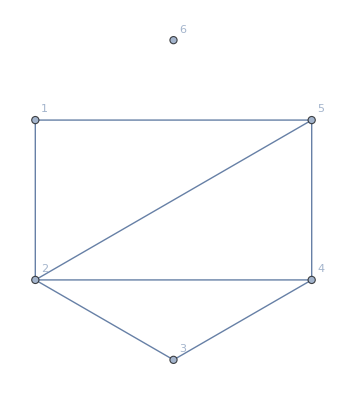

```mathematica
Select[Map[First,PrintLength[Tally[PrintLength[ShowGraphsFor3Three[6,4],"all graphs"],IsomorphicGraphQ],"isomorphic"]],Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]==13&]
```

Length is 4096 all graphs

Length is 226 isomorphic

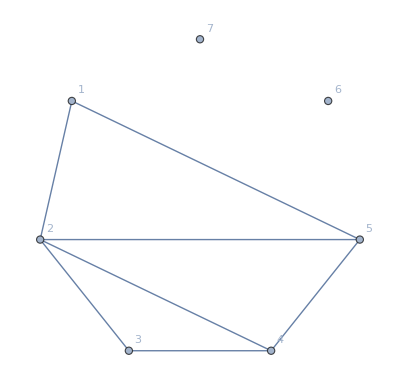

```mathematica
Select[Map[First,PrintLength[Tally[PrintLength[ShowGraphsFor3Three[7,16],"all graphs"],IsomorphicGraphQ],"isomorphic"]],Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]==55&]
```

```mathematica
TableForm[
Monitor[
Table[
With[
{count=Length[quad1[nodes]]},
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,Map[First,PrintLength[Tally[PrintLength[ShowGraphsFor3Four[nodes,count],"all graphs"],IsomorphicGraphQ],"isomorphic"]]]//Tally//Sort
],
{nodes,5,7}
],
nodes],
TableDepth->1
]
```

Length is 1 all graphs

Length is 1 isomorphic

Length is 256 all graphs

Length is 16 isomorphic

Length is 65536 all graphs

Length is 240 isomorphic

{{4,1}}
{{7,1},{8,3},{9,2},{11,4},{12,2},{15,3},{19,1}}
{{7,4},{8,6},{9,4},{10,4},{11,5},{12,7},{13,8},{14,14},{15,4},{16,8},{17,9},{18,15},{19,3},{20,8},{21,11},{22,3},{23,2},{24,2},{25,18},{26,12},{27,2},{28,9},{29,9},{30,5},{31,2},{32,2},{33,3},{34,3},{36,18},{38,1},{39,3},{40,8},{41,5},{47,4},{51,12},{52,1},{53,1},{66,4},{85,1}}

```mathematica
262144*64
```

16777216

```mathematica
TableForm[
Monitor[
Table[
With[
{count=Length[quad1[nodes]]},
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,Map[First,Tally[ShowGraphsFor3Three[nodes,count],IsomorphicGraphQ]]]//Tally//Sort
],
{nodes,5,8}
],
nodes],
TableDepth->1
]
```

$Aborted

```mathematica
TableForm[
Monitor[
Table[
With[
{count=Length[quad1[nodes]]},
Print[count, " per item (", nodes, ") expecting ", count^5];
Map[Length[Select[FindFullFormula[#],SymbolLevel[#]==4&]]&,Map[First,PrintLength[Tally[PrintLength[ShowGraphsFor3[nodes,count],"all graphs"],IsomorphicGraphQ],"isomorphic"]]]//Tally//Sort
],
{nodes,5,7}
],
nodes],
TableDepth->1
]
```

1 per item (5) expecting 1

Length is 1 all graphs

Length is 1 isomorphic

4 per item (6) expecting 1024

Length is 1024 all graphs

Length is 6 isomorphic

16 per item (7) expecting 1048576

Length is 1048576 all graphs

Length is 81 isomorphic

{{5,1}}
{{11,1},{12,1},{15,1},{16,1},{20,1},{25,1}}
{{11,2},{13,1},{14,1},{15,1},{16,2},{17,2},{19,3},{20,5},{23,2},{24,5},{26,1},{27,3},{28,7},{31,2},{32,2},{35,8},{38,1},{39,4},{40,4},{43,2},{44,2},{46,1},{50,5},{52,1},{54,1},{55,4},{65,1},{70,4},{71,1},{90,2},{115,1}}